## Lineare Gleichung

```mathematica
Manipulate[Plot[a*x+ b , {x, -10,10},PlotLabel->a*x+ b , PlotRange-> {{-10,10}, {-10,10}}],{a,-4,4,0.25}, {b,-4,4,0.25}]
```

## Quadratische Gleichung

```mathematica
Manipulate[Plot[a*x^2+ b x +c, {x, -4,4},PlotLabel->a*x^2+ b x +c,PlotRange-> {{-4,4}, {-10,10}}],{a,-4,4,0.25}, {b,-4,4,0.25},{c,-4,4,0.25}]
```

## Bruchgleichung

```mathematica
Manipulate[Plot[a*x+ b , {x, -10,10},PlotLabel->a*x+ b , PlotRange-> {{-10,10}, {-10,10}}],{a,-4,4,0.25}, {b,-4,4,0.25}]
```

## Monom

```mathematica
Manipulate[Plot[x^n , {x, -10,10},PlotLabel->x^n , PlotRange-> {{-10,10}, {-10,10}}],{n,0,10,1}]
```

## Polynom mit ganzrationalen Zahlen

```mathematica
Manipulate[Plot[a*x^5 +b*x^4+ c*x^3+d*x^2+e*x + f, {x, -10,10},PlotLabel->a*x^5 +b*x^4+ c*x^3+d*x^2+d*x + e , PlotRange-> {{-10,10}, {-10,10}}],{a,-4,4,0.25}, {b,-4,4,0.25},{c,-4,4,0.25}, {d,-4,4,0.25},{e,-4,4,0.25},{f,-4,4,0.25}]
```

## Polynom mit gebrochen rationalen Zahlen

```mathematica
Manipulate[Plot[(a*x^2+b*x + c)/(d*x^2+e*x + f), {x, -10,10},PlotLabel->(a*x^2+b*x + c)/(d*x^2+e*x + f) , PlotRange-> {{-10,10}, {-10,10}}],{a,-4,4,0.25}, {b,-4,4,0.25},{c,-4,4,0.25}, {d,-4,4,0.25},{e,-4,4,0.25},{f,-4,4,0.25}]
```

## Potzenzfunktion

```mathematica
Manipulate[Plot[x^a, {x, -10,10},PlotLabel->x^a, PlotRange-> {{-10,10}, {-10,10}}],{a,-4,4,0.25}]
```

## Exponentialfunktion

```mathematica
Manipulate[Plot[Exp[a*x], {x, -10,10},PlotLabel->Exp[a*x], PlotRange-> {{-10,10}, {-10,10}}],{a,-4,4,0.25}]
```

## Logarithmusfunktion

```mathematica
Manipulate[Plot[Log[a,x], {x, -10,10},PlotLabel->Log[a,x], PlotRange-> {{0,10}, {-20,20}}],{a,0,4,0.1}]
```

## Betragsfunktion

```mathematica
Manipulate[Plot[Abs[a*x +b], {x, -30,30},PlotLabel->Abs[a*x +b], PlotRange-> {{-30,30}, {-10,10}}],{a,-2,2,0.1},{b,-8,4,0.1}]
```

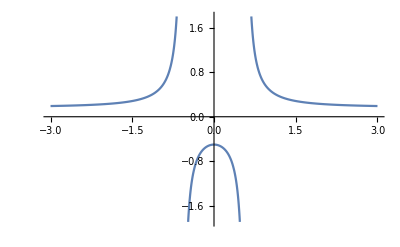

```mathematica
Plot[(x^2+1)/(6x^2-2),{x,-3,3}]
```

## Trigonometrische Funktionen

```mathematica
Manipulate[Plot[a*Sin[x +b], {x, -30,30},PlotLabel->a*Sin[x +b], PlotRange-> {{-30,30}, {-10,10}}],{a,-4,4,0.1},{b,-2π,2 π,0.25*π}]
```

```mathematica
Manipulate[Plot[a*Cos[x +b], {x, -30,30},PlotLabel->a*Cos[x +b], PlotRange-> {{-30,30}, {-10,10}}],{a,-4,4,0.1},{b,-2π,2 π,0.25*π}]
```

```mathematica
Manipulate[Plot[a*Tan[x +b], {x, -30,30},PlotLabel->a*Tan[x +b], PlotRange-> {{-30,30}, {-10,10}}],{a,-4,4,0.1},{b,-2π,2 π,0.25*π}]
```

## Hyperbolische Funktionen

```mathematica
Manipulate[Plot[a*Sinh[x +b], {x, -30,30},PlotLabel->a*Sinh[x +b], PlotRange-> {{-30,30}, {-10,10}}],{a,-4,4,0.1},{b,-2π,2 π,0.25*π}]
```

## Verknüpfung von Funktionen

```mathematica
g[x_]:=0.5*x^2+3;
f[x_]:=Exp[x];
```

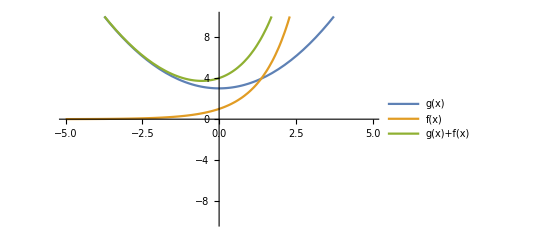

```mathematica
Plot[{g[x],f[x],f[x]+g[x]} , {x, -5,5},PlotLegends->{"g(x)","f(x)","g(x)+f(x)"}, PlotRange-> {{-5,5}, {-10,10}}]
```

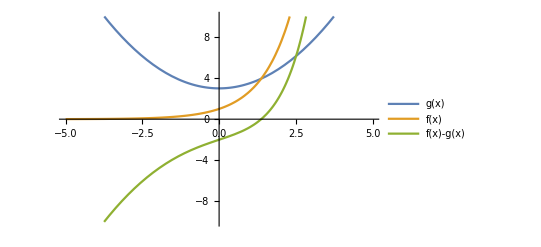

```mathematica
Plot[{g[x],f[x],f[x]-g[x]} , {x, -5,5},PlotLegends->{"g(x)","f(x)","f(x)-g(x)"}, PlotRange-> {{-5,5}, {-10,10}}]
```

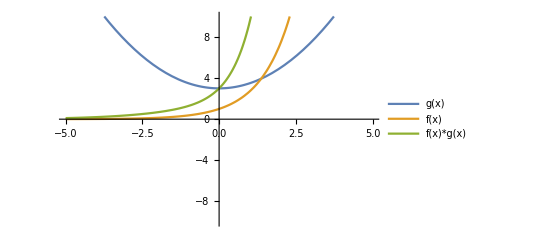

```mathematica
Plot[{g[x],f[x],f[x]*g[x]} , {x, -5,5},PlotLegends->{"g(x)","f(x)","f(x)*g(x)"}, PlotRange-> {{-5,5}, {-10,10}}]
```

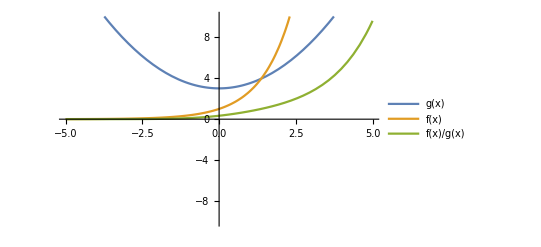

```mathematica
Plot[{g[x],f[x],f[x]/g[x]} , {x, -5,5},PlotLegends->{"g(x)","f(x)","f(x)/g(x)"}, PlotRange-> {{-5,5}, {-10,10}}]
```

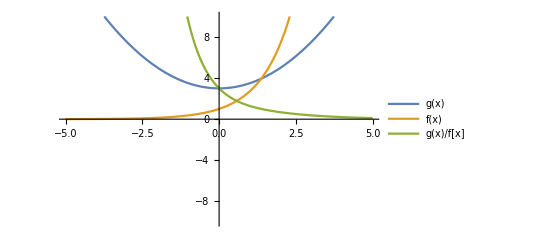

```mathematica
Plot[{g[x],f[x],g[x]/f[x]} , {x, -5,5},PlotLegends->{"g(x)","f(x)","g(x)/f[x]"}, PlotRange-> {{-5,5}, {-10,10}}]
```

## Taylorreihe

## Exponentialfunktion

```mathematica
f[x_]:=Exp[x];
t1[x_]:=1+x;
t2[x_]:=1+x+x^2/2;
t3[x_]:=1+x+x^2/2+x^3/6;
t4[x_]:=1+x+x^2/2+x^3/6+x^4/24;
t5[x_]:=1+x+x^2/2+x^3/6+x^4/24+x^5/120;
t6[x_]:=1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720;
t7[x_]:=1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040;
t9[x_]:=1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880;
```

```mathematica
Series[Exp[x], {x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

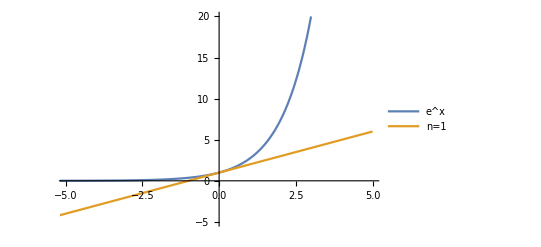

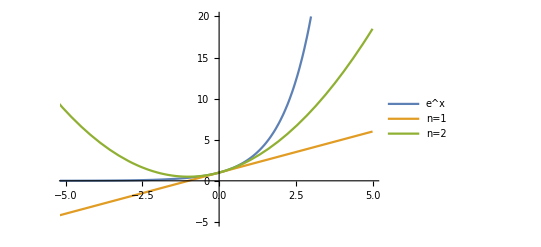

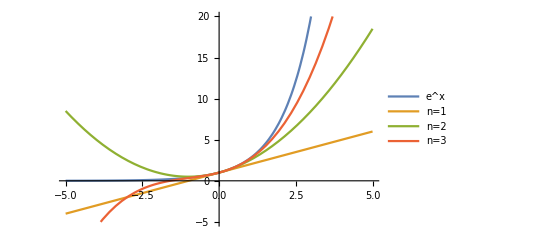

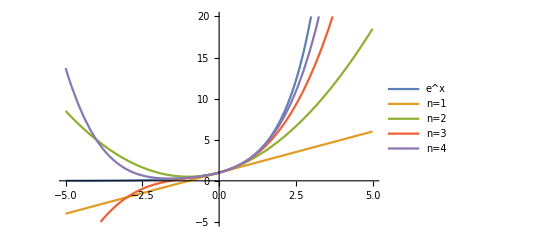

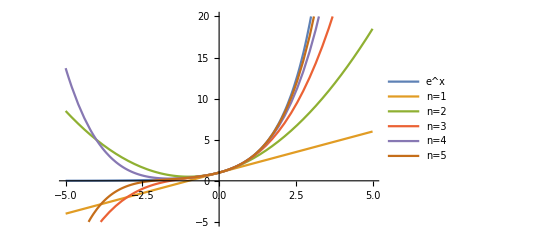

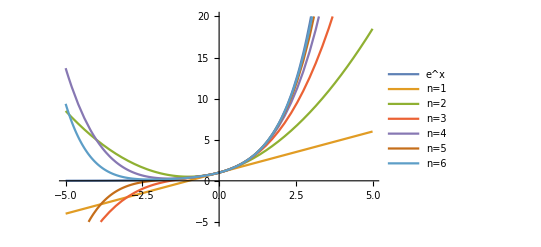

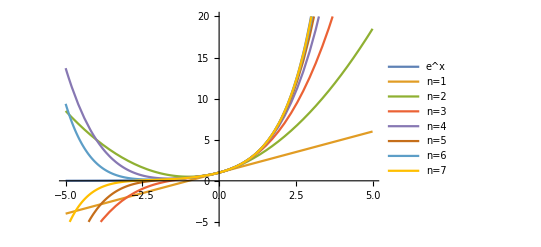

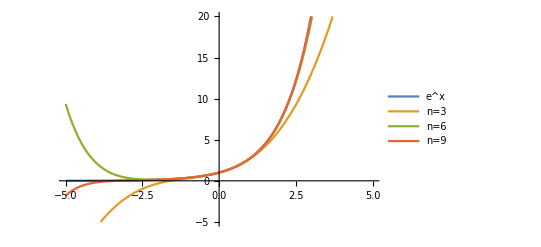

```mathematica
Plot[{f[x],t1[x]},{x,-10,5},PlotLegends->{"e^x","n=1"},PlotRange-> {{-5,5}, {-5,20}}]
Plot[{f[x],t1[x],t2[x]},{x,-10,5},PlotLegends->{"e^x","n=1","n=2"},PlotRange-> {{-5,5}, {-5,20}}]
Plot[{f[x],t1[x],t2[x],t3[x]},{x,-5,5},PlotLegends->{"e^x","n=1","n=2","n=3"},PlotRange-> {{-5,5}, {-5,20}}]
Plot[{f[x],t1[x],t2[x],t3[x],t4[x]},{x,-5,5},PlotLegends->{"e^x","n=1","n=2","n=3","n=4"},PlotRange-> {{-5,5}, {-5,20}}]
Plot[{f[x],t1[x],t2[x],t3[x],t4[x],t5[x]},{x,-5,5},PlotLegends->{"e^x","n=1","n=2","n=3","n=4","n=5"},PlotRange-> {{-5,5}, {-5,20}}]
Plot[{f[x],t1[x],t2[x],t3[x],t4[x],t5[x],t6[x]},{x,-5,5},PlotLegends->{"e^x","n=1","n=2","n=3","n=4","n=5","n=6"},PlotRange-> {{-5,5}, {-5,20}}]
Plot[{f[x],t1[x],t2[x],t3[x],t4[x],t5[x],t6[x],t7[x]},{x,-5,5},PlotLegends->{"e^x","n=1","n=2","n=3","n=4","n=5","n=6","n=7"},PlotRange-> {{-5,5}, {-5,20}}]
Plot[{f[x],t3[x],t6[x],t9[x]},{x,-5,5},PlotLegends->{"e^x","n=3","n=6","n=9"},PlotRange-> {{-5,5}, {-5,20}}]
Plot[{f[x],t9[x]},{x,-5,5},PlotLegends->{"e^x","n=9"},PlotRange-> {{-5,5}, {-5,20}}]
```

## Logarithmus und Konvergenzradius

```mathematica
g[x_]:=Log[1+x];
l4[x_]:=x-x^2/2+x^3/3-x^4/4;
l8[x_]:=-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8;
l12[x_]:=x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+x^11/11-x^12/12;
l13[x_]:=x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+x^11/11-x^12/12+x^13/13;
l24[x_]:=x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+x^11/11-x^12/12+x^13/13-x^14/14+x^15/15-x^16/16+x^17/17-x^18/18+x^19/19-x^20/20+x^21/21-x^22/22+x^23/23-x^24/24;
```

```mathematica
Series[Log[1+x], {x,0,24}]
```

x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+x^11/11-x^12/12+x^13/13-x^14/14+x^15/15-x^16/16+x^17/17-x^18/18+x^19/19-x^20/20+x^21/21-x^22/22+x^23/23-x^24/24+O[x]^25

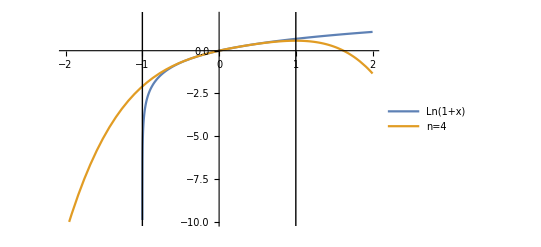

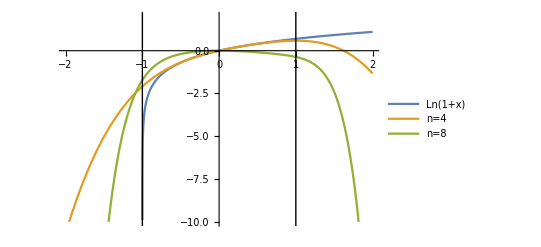

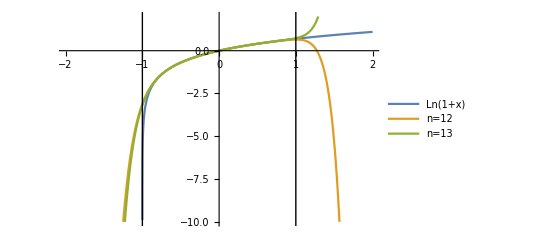

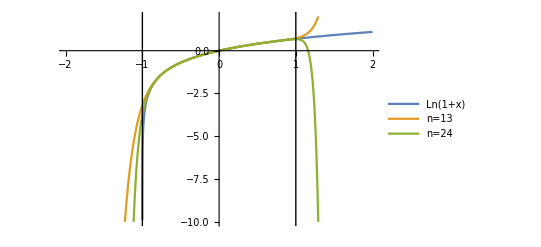

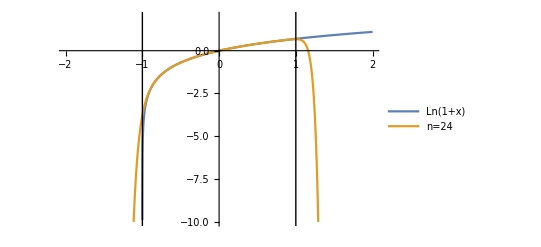

```mathematica
Plot[{g[x],l4[x]},{x,-2,2},PlotLegends->{"Ln(1+x)","n=4"},PlotRange-> {{-2,2}, {-10,2}}, Epilog->{InfiniteLine[{-1,0},{0,1}],InfiniteLine[{1,0},{0,1}]}]
Plot[{g[x],l4[x],l8[x]},{x,-2,2},PlotLegends->{"Ln(1+x)","n=4","n=8"},PlotRange-> {{-2,2}, {-10,2}},Epilog->{InfiniteLine[{-1,0},{0,1}],InfiniteLine[{1,0},{0,1}]}]
Plot[{g[x],l12[x],l13[x]},{x,-2,2},PlotLegends->{"Ln(1+x)","n=12","n=13"},PlotRange-> {{-2,2}, {-10,2}},Epilog->{InfiniteLine[{-1,0},{0,1}],InfiniteLine[{1,0},{0,1}]} ]
Plot[{g[x],l13[x],l24[x]},{x,-2,2},PlotLegends->{"Ln(1+x)","n=13","n=24"},PlotRange-> {{-2,2}, {-10,2}}, Epilog->{InfiniteLine[{-1,0},{0,1}],InfiniteLine[{1,0},{0,1}]}]
Plot[{g[x],l24[x]},{x,-2,2},PlotLegends->{"Ln(1+x)","n=24"},PlotRange-> {{-2,2}, {-10,2}}, Epilog->{InfiniteLine[{-1,0},{0,1}],InfiniteLine[{1,0},{0,1}]}]
```